{a→-3.96624×10^-9,b→-0.000414276}

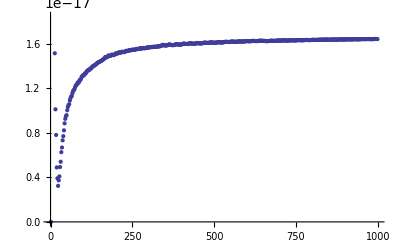

```mathematica
(* Horizontal test *)
ErrHorizontal = Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_horizontal.csv"];
ErrAjusteH = FindFit[ErrHorizontal,a(1- Exp[-b  x]),{a,b},x,Method->NMinimize]
Show[
ListPlot[ErrHorizontal],
Plot[a(1- Exp[-b  x])/. ErrAjusteH,{x,0,1000},PlotStyle->Thick]
]
```

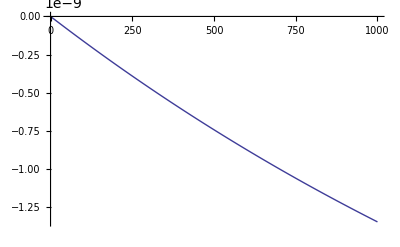

```mathematica
Plot[a(1- Exp[b x])/. ErrAjusteH,{x,0,1000},PlotStyle->Thick]
```

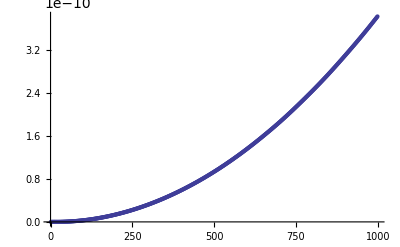

```mathematica
(* Vertical test *)
ErrVertical = Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_vertical.csv"];
ListPlot[ErrVertical]
```

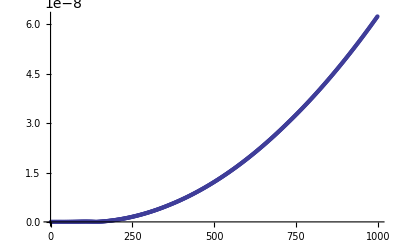

```mathematica
(* Diagonal ne test *)
ErrDiagonalNE= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_ne.csv"];
ListPlot[ErrDiagonalNE]
```

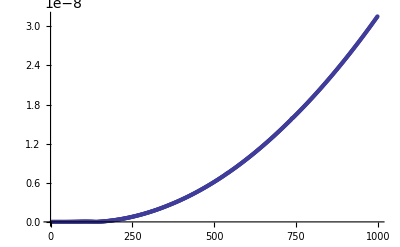

```mathematica
(* Diagonal se test *)
ErrDiagonalSE= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_se.csv"];
ListPlot[ErrDiagonalSE]
```

0.0824325/x^2

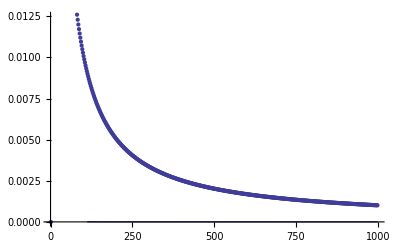

```mathematica
(* Linear test *)
ErrDiagonalL= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_l.csv"];
ErrAjusteL = Fit[ErrDiagonalL,{1/x^2},x]
Show[
ListPlot[ErrDiagonalL],
Plot[ErrAjusteL,{x,0,1000}]
]
```

```mathematica
ErrAjusteL[50000]
```

5.80909×10^-6

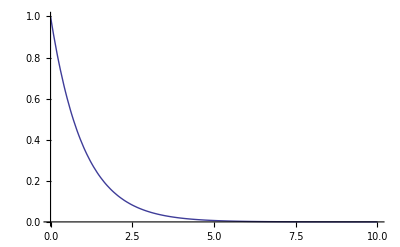

```mathematica
Plot[Exp[-x],{x,0,10},PlotRange->Full]
```